```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=10;
PI=N[π,12];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
```

## Basis

```mathematica
States=Table[{},{nN,1,2^(numQb/2)}];
Do[(
B=IntegerDigits[n-1,2,numQb];
circ=Table[If[B[[k+1]]==1,Subscript[X, k],Subscript[Z, k]],{k,0,numQb-1,1}];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Round[Abs[GetQuregMatrix[ψOUT]]];
index=Position[OUT,1][[1,1]];

BN=Table[B[[k+1]],{k,0,numQb-1,2}];
nN=FromDigits[BN,2]+1;
AppendTo[States[[nN]],index];
),{n,1,2^numQb}];
States;
```

```mathematica
ProNeurons[OUT_]:=(
Pro=Table[
P=0;
Do[P=P+OUT[[States[[i,j]]]],{j,1,2^(numQb/2)}];
P
,{i,1,2^(numQb/2)}];
Return[Pro]
)
```

## Neural Network Cirucit

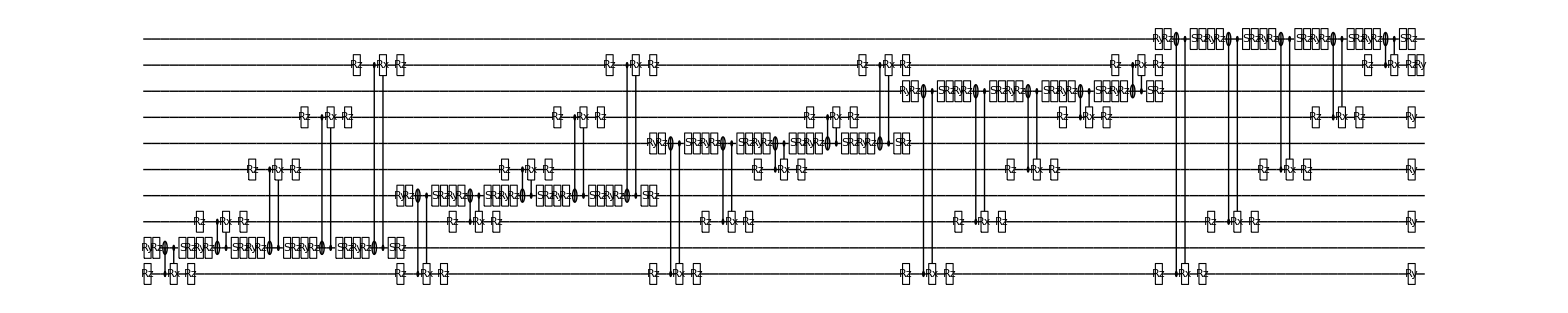

```mathematica
circuitNN[θlist_]:=(
circNN={};
Do[(
j=(b+1)/2;
Do[(
i=(a+2)/2;
ϕ=θlist[[numQb(j-1)+2i-1]];
θ=θlist[[numQb(j-1)+2i]];
circMR={Subscript[Rz, a][θ],Subscript[Rz, b][θ],Subscript[C, a][Subscript[X, b]],Subscript[C, b][Subscript[Rx, a][PI-2θ]],Subscript[S, b],Subscript[Rz, b][-θ],Subscript[Rz, a][-θ]};
circNN=Join[circNN,{Subscript[Ry, b][ϕ]},circMR];
),{a,0,numQb-1,2}]
),{b,1,numQb-1,2}];
Do[(
i=(a+2)/2;
ϕ=θlist[[numQb^2/2+i]];
circNN=Join[circNN,{Subscript[Ry, a][ϕ]}];
),{a,0,numQb-1,2}];
Return[circNN]
)
circNN=circuitNN[Table[i/100,{i,1,(numQb+1)numQb/2}]];
DrawCircuit@circNN
```

## Distance

-Graphics-

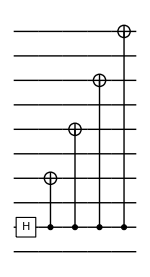

-Graphics-

```mathematica
circNeurons=Table[Subscript[H, i],{i,0,numQb-1,2}];
DrawCircuit@circNeurons
circGHZ={Subscript[H, 1]};Do[AppendTo[circGHZ,Subscript[C, 1][Subscript[X, i]]],{i,3,numQb-1,2}];
DrawCircuit@circGHZ
circPLUS=Table[Subscript[H, i],{i,1,numQb-1,2}];
DrawCircuit@circPLUS
```

```mathematica
Clear[Distance]
Distance[θlist_/;(And@@(NumericQ/@θlist))]:=(
circNN=circuitNN[θlist];

circ=Join[circNeurons,circGHZ,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProGHZ=ProNeurons[OUT];

circ=Join[circNeurons,circPLUS,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProPLUS=ProNeurons[OUT];

Dis=Total[Abs[ProGHZ-ProPLUS]]/2;

Return[Dis]
)
Distance[Table[0,{i,1,(numQb+1)numQb/2}]]
ProGHZ
ProPLUS
```

0.9375

{0.5,1.21855×10^-32,2.8116×10^-65,6.3261×10^-65,2.63545×10^-98,1.31773×10^-98,1.05418×10^-97,6.58863×10^-98,4.94068×10^-131,1.38912×10^-194,2.77824×10^-195,1.85246×10^-163,9.88136×10^-131,4.94068×10^-131,7.40984×10^-163,4.94068×10^-131,0.5,1.21855×10^-32,2.8116×10^-65,6.3261×10^-65,2.63545×10^-98,1.31773×10^-98,1.05418×10^-97,6.58863×10^-98,4.94068×10^-131,1.38912×10^-194,2.77824×10^-195,1.85246×10^-163,9.88136×10^-131,4.94068×10^-131,7.40984×10^-163,4.94068×10^-131}

{0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125}

## Find

Sometimes the optimisation fails, which seems to be an issue caused by a bad random seed. Just try again.

{0.968246,{0_1→2.30566×10^-8,0_2→-1.17325×10^-7,0_3→4.00545×10^-8,0_4→4.36523×10^-8,0_5→-3.87525×10^-8,0_6→3.97523×10^-9,0_7→6.29057×10^-8,0_8→2.76391×10^-7,0_9→-1.3997×10^-6,0_10→-2.53563×10^-7,0_11→-4.06062×10^-8,0_12→-1.87689×10^-7,0_13→0.785392,0_14→-2.05043×10^-7,0_15→-2.87713×10^-8,0_16→1.65175×10^-10,0_17→-1.92331×10^-7,0_18→8.57391×10^-9,0_19→9.31682×10^-7,0_20→-2.14909×10^-6,0_21→5.83625×10^-8,0_22→3.4793×10^-7,0_23→0.785399,0_24→3.97044×10^-10,0_25→-2.18627,0_26→-1.83699×10^-7,0_27→8.86523×10^-8,0_28→3.02224×10^-7,0_29→1.12821×10^-7,0_30→-2.0896×10^-6,0_31→-4.35337×10^-8,0_32→-2.82803×10^-6,0_33→0.785397,0_34→-4.70777×10^-8,0_35→-1.5708,0_36→-3.1034×10^-7,0_37→-0.615532,0_38→-3.72814×10^-7,0_39→-7.33173×10^-9,0_40→-8.76662×10^-7,0_41→-1.56899×10^-8,0_42→2.16953×10^-6,0_43→0.0161323,0_44→-1.40874×10^-7,0_45→-1.05846,0_46→-5.11355×10^-8,0_47→-0.13332,0_48→-1.22038×10^-7,0_49→0.987445,0_50→-3.0822×10^-7,0_51→-0.453342,0_52→0.180585,0_53→1.01424,0_54→0.578482,0_55→0.583311}}

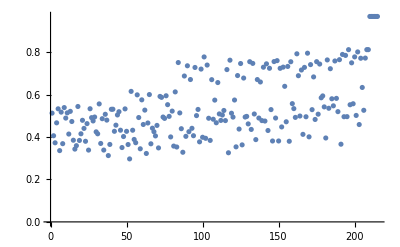

```mathematica
θlist=Table[Subscript[θ, i],{i,1,(numQb+1)numQb/2}];
{res,data}=Reap[NMaximize[Distance[θlist],θlist,EvaluationMonitor:>Sow[Distance[θlist]]]];
res
plot=ListPlot[data]
```

## Optimal Parameters

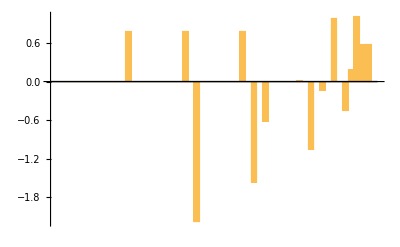

0.968246

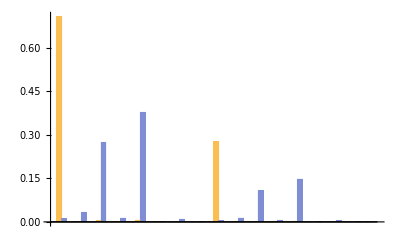

```mathematica
plotθlist=BarChart[θlist/.Last[res]]
Distance[θlist/.Last[res]]
ProGP=Table[{ProGHZ[[i]],ProPLUS[[i]]},{i,1,2^(numQb/2)}];
plotPro=BarChart[ProGP]
```

## Data and Plot

```mathematica
file=File["Ising_find.dat"];
toFile={};
AppendTo[toFile,"Optimal distance:"];
AppendTo[toFile,res[[1]]];
AppendTo[toFile,""];
AppendTo[toFile,"Optimal parameters:"];
AppendTo[toFile,θlist/.Last[res]];
AppendTo[toFile,""];
AppendTo[toFile,"Evaluations:"];
AppendTo[toFile,data];
AppendTo[toFile,""];
Export[file,toFile];
```

```mathematica
DisC=N[2(1/2-1/2^(numQb/2))+(2^(numQb/2)-2)/2^(numQb/2),12]/2
Fid=N[(1/(√2))^(numQb/2-1),12]
DisQ=N[√(1-Fid^2),12]
```

0.9375

0.25

0.968245836552

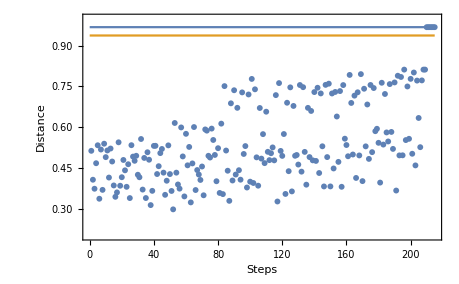

```mathematica
plot=ListPlot[Transpose[{Range[1,Length[data[[1]]]],data[[1]]}],PlotRange->{{0,Length[data[[1]]]},{0.2,1}},Axes->{False,False},Frame->True,FrameLabel->{"Steps","Distance"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotQC=ListLinePlot[{{{0,DisQ},{Length[data[[1]]],DisQ}},{{0,DisC},{Length[data[[1]]],DisC}}}];
Show[plot,plotQC]
```